```mathematica
Clear[f]
μ=1;
f[y_,θ_,B_,J_]:=-θ*Log[2]-θ*Log[Φ[y,θ,B,J]]

Φ[y_,θ_,B_,J_]:=Exp[-(J/θ)*y^2/2]*Cosh[(J/θ)*y+μ*B/θ]
```

```mathematica
llimit=0.99;
ulimit=1.01;
llimitJ=0.95;
ulimitJ=1.05;
theta=Table[j,{j,llimit,ulimit,0.0005}];
B=0.0001;
Jrange=Table[j,{j,llimitJ,ulimitJ,0.0005}];
y2d={};
f2d={};
percentcompleted=0;
For[j=1,j≤Length[theta],j++,
row={};
percentcompletednew=Round[100*j/Length[theta],5];
If[Mod[percentcompleted,10]==0&&percentcompleted≠percentcompletednew,Print[percentcompleted]];
For[k=1,k≤Length[Jrange],k++,
θ=theta[[j]];
J=Jrange[[k]];
B=0.0001;
ynum=FindRoot[y==Tanh[(J/θ)*y+B/θ],{y,0.5}][[1]][[2]];
fnum=f[ynum,θ,B,J];
AppendTo[row,ynum];
AppendTo[f2d,{θ,N,fnum}];
];
AppendTo[y2d,row];
percentcompleted=percentcompletednew;
]
```

0

10

20

30

40

50

60

70

80

90

```mathematica
y=ListInterpolation[Transpose[y2d],{{llimitJ,ulimitJ},{llimit,ulimit}}]
```

InterpolatingFunction[{{0.95, 1.05}, {0.99, 1.01}}, <>]

```mathematica
Clear[j,θ]
B=0.0001;
df1=Table[{jj,(D[f[y[j,θ],θ,B,j]/.θ->1.0,j])/.j->jj},{jj,llimitJ,ulimitJ,0.0005}];
ds1=Table[{jj,-(D[D[f[y[j,θ],θ,B,j],θ]/.θ->1.0,j])/.(j->jj)},{jj,llimitJ,ulimitJ,0.0005}];
η1=Table[{ds1[[j]][[1]],ds1[[j]][[2]]/df1[[j]][[2]]},{j,1,Length[ds1]}];
```

```mathematica
llimit=0.99;
ulimit=1.01;
llimitJ=0.95;
ulimitJ=1.05;
theta=Table[j,{j,llimit,ulimit,0.0005}];
B=0.0005;
Jrange=Table[j,{j,llimitJ,ulimitJ,0.0005}];
y2d={};
f2d={};
percentcompleted=0;
For[j=1,j≤Length[theta],j++,
row={};
percentcompletednew=Round[100*j/Length[theta],5];
If[Mod[percentcompleted,10]==0&&percentcompleted≠percentcompletednew,Print[percentcompleted]];
For[k=1,k≤Length[Jrange],k++,
θ=theta[[j]];
J=Jrange[[k]];
B=0.0005;
ynum=FindRoot[y==Tanh[(J/θ)*y+B/θ],{y,0.5}][[1]][[2]];
fnum=f[ynum,θ,B,J];
AppendTo[row,ynum];
AppendTo[f2d,{θ,N,fnum}];
];
AppendTo[y2d,row];
percentcompleted=percentcompletednew;
]
```

0

10

20

30

40

50

60

70

80

90

```mathematica
y=ListInterpolation[Transpose[y2d],{{llimitJ,ulimitJ},{llimit,ulimit}}]
```

InterpolatingFunction[{{0.95, 1.05}, {0.99, 1.01}}, <>]

```mathematica
Clear[j,θ]
B=0.0005;
df2=Table[{jj,(D[f[y[j,θ],θ,B,j]/.θ->1.0,j])/.j->jj},{jj,llimitJ,ulimitJ,0.0005}];
ds2=Table[{jj,-(D[D[f[y[j,θ],θ,B,j],θ]/.θ->1.0,j])/.(j->jj)},{jj,llimitJ,ulimitJ,0.0005}];
η2=Table[{ds2[[j]][[1]],ds2[[j]][[2]]/df2[[j]][[2]]},{j,1,Length[ds2]}];
```

```mathematica
llimit=0.99;
ulimit=1.01;
llimitJ=1.0005;
ulimitJ=1.05;
theta=Table[j,{j,llimit,ulimit,0.0005}];
B=0.000;
Jrange=Table[j,{j,llimitJ,ulimitJ,0.0005}];
y2d={};
f2d={};
percentcompleted=0;
For[j=1,j≤Length[theta],j++,
row={};
percentcompletednew=Round[100*j/Length[theta],5];
If[Mod[percentcompleted,10]==0&&percentcompleted≠percentcompletednew,Print[percentcompleted]];
For[k=1,k≤Length[Jrange],k++,
θ=theta[[j]];
J=Jrange[[k]];
B=0.000;
ynum=FindRoot[y==Tanh[(J/θ)*y+B/θ],{y,0.5}][[1]][[2]];
fnum=f[ynum,θ,B,J];
AppendTo[row,ynum];
AppendTo[f2d,{θ,N,fnum}];
];
AppendTo[y2d,row];
percentcompleted=percentcompletednew;
]
```

0

10

20

30

40

50

60

70

80

90

```mathematica
y=ListInterpolation[Transpose[y2d],{{llimitJ,ulimitJ},{llimit,ulimit}}]
```

InterpolatingFunction[{{1.0005, 1.05}, {0.99, 1.01}}, <>]

```mathematica
Clear[j,θ]
B=0.000;
df3=Table[{jj,(D[f[y[j,θ],θ,B,j]/.θ->1.0,j])/.j->jj},{jj,llimitJ,ulimitJ,0.0005}];
ds3=Table[{jj,-(D[D[f[y[j,θ],θ,B,j],θ]/.θ->1.0,j])/.(j->jj)},{jj,llimitJ,ulimitJ,0.0005}];
η3=Table[{ds3[[j]][[1]],ds3[[j]][[2]]/df3[[j]][[2]]},{j,1,Length[ds3]}];
```

```mathematica
Clear[μ,B,θ,K]
h=μ*B/θ;
K=J/θ;
```

```mathematica
Clear[y,θ,B,J]
Normal[Series[Tanh[J/θ*y],{y,0,3},{B,0,1}]]

s=Solve[y==-(J^3 y^3)/(3 θ^3)+(J y)/θ,{y}]
```

-(J^3 y^3)/(3 θ^3)+(J y)/θ

{{y→0},{y→-(√3 √(J θ^2-θ^3))/J^(3/2)},{y→(√3 √(J θ^2-θ^3))/J^(3/2)}}

```mathematica
yan[J_,θ_]:=(√3 √(J θ^2-θ^3))/J^(3/2)
```

```mathematica
ypos[J_,θ_]:=(√3 √(J θ^2-θ^3))/J^(3/2)
yneg[J_,θ_,B_]:=(mu*B)/(θ-J)
```

```mathematica
Clear[j,θ]
B=0.0001;
dfP=Table[{jj,(D[f[ypos[j,θ],θ,0,j]/.θ->1.0,j])/.j->jj},{jj,1.0,ulimitJ,0.0001}];
dsP=Table[{jj,-(D[D[f[ypos[j,θ],θ,0,j],θ]/.θ->1.0,j])/.(j->jj)},{jj,1.0,ulimitJ,0.0001}];
ηP=Table[{dsP[[j]][[1]],dsP[[j]][[2]]/dfP[[j]][[2]]},{j,1,Length[dsP]}];

dfN=Table[{jj,(D[f[yneg[j,θ,B],θ,B,j]/.θ->1.0,j])/.j->jj},{jj,llimitJ,0.995,0.0001}];
dsN=Table[{jj,-(D[D[f[yneg[j,θ,B],θ,B,j],θ]/.θ->1.0,j])/.(j->jj)},{jj,llimitJ,0.995,0.0001}];
ηN=Table[{dsN[[j]][[1]],dsN[[j]][[2]]/dfN[[j]][[2]]},{j,1,Length[dsN]}];
```

```mathematica
etaP=Table[{j,1/(j-1)},{j,1.0001,1.05,0.0001}];
etaN=Table[{j,-2/(j-1)},{j,0.95,1.0,0.0001}];
```

Power::infy: Infinite expression 1/0. encountered.

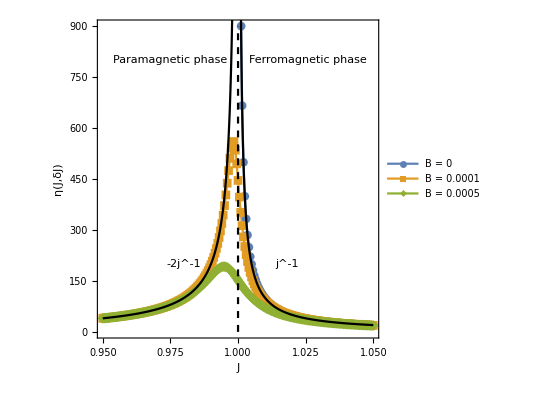

```mathematica
pl=Show[ListPlot[{η3,η1,η2},Joined->True,Frame->True,FrameStyle->Thick,AspectRatio->1,BaseStyle->Medium,FrameLabel->{"J","η(J,δJ)"},PlotLegends->{"B = 0","B = 0.0001","B = 0.0005"},Epilog->{Inset["Paramagnetic phase",{0.975,800}],Inset["Ferromagnetic phase",{1.026,800}],Inset["-2j^-1",{0.98,200}],Inset["j^-1",{1.018,200}]},PlotMarkers->Automatic,PlotRange->{Full,{0,900}}],ListPlot[etaN,PlotStyle->Black,Joined->True,PlotRange->Full],ListLinePlot[{{1.0,0},{1.0,900}},PlotStyle->{Black,Dashed}],
ListPlot[etaP,PlotStyle->Black,Joined->True,PlotRange->Full]]
```